```mathematica
Integrate[Sin[x]Exp[- x],{x,0,∞}]
```

1/2

```mathematica
Integrate[Sin[x]Exp[- x],{x,0,1}]
%*1.
```

-(-ⅇ+Cos[1]+Sin[1])/(2 ⅇ)

0.245837

```mathematica
D[c1/(λ^5(Exp[c2/(λ T)]-1)),T]
%//Simplify
%//FortranForm
%//FullSimplify
```

(c1 c2 ⅇ^(c2/(T λ)))/((-1+ⅇ^(c2/(T λ)))^2 T^2 λ^6)

(c1 c2 ⅇ^(c2/(T λ)))/((-1+ⅇ^(c2/(T λ)))^2 T^2 λ^6)

(c1 c2 Csch[c2/(2 T λ)]^2)/(4 T^2 λ^6)

(c1*c2*E**(c2/(T*λ)))/((-1 + E**(c2/(T*λ)))**2*T**2*λ**6)

```mathematica
h=6.62607004*10^-34
c0=299792458
2*π*h*c0^2
k=1.38064852*10^-23
h c0/k
c1=3.74177118*10^-16;
c2=14387.75225*10^-6;
eb[λ_,T_]=c1/(λ^5(Exp[c2/(λ T)]-1));
ebdt[λ_,T_]=D[c1/(λ^5(Exp[c2/(λ T)]-1)),T];
```

6.62607×10^-34

299792458

3.74177×10^-16

1.38065×10^-23

0.0143878

0.0143878

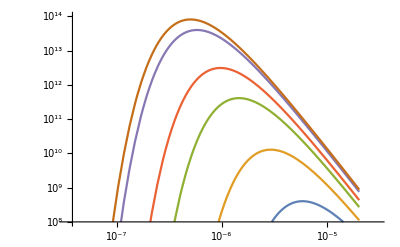

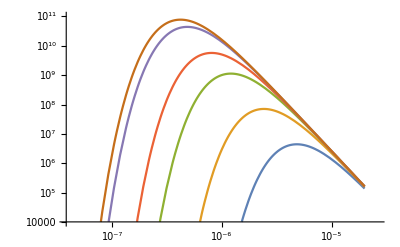

```mathematica
LogLogPlot[{eb[λ,500],eb[λ,1000],eb[λ,2000],eb[λ,3000],eb[λ,5000],eb[λ,5762]},{λ,0.5*10^-7,20*10^-6},PlotRange->{10^8,10^14}]

LogLogPlot[{ebdt[λ,500],ebdt[λ,1000],ebdt[λ,2000],ebdt[λ,3000],ebdt[λ,5000],ebdt[λ,5762]},{λ,0.5*10^-7,20*10^-6},PlotRange->{10^4,10^11}]
```

```mathematica
eb[0.0000029,1000.0]
```

1.2867×10^25

```mathematica
NIntegrate[ebdt[λ,2911],{λ,0,∞}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in λ near {λ} = {4.64278×10^-7}. NIntegrate obtained 5595. and 0.15237 for the integral and error estimates.

5595.

```mathematica
NIntegrate[eb[λ,2911],{λ,0,∞}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in λ near {λ} = {1.48905×10^-6}. NIntegrate obtained 4.07176×10^6 and 36.8657 for the integral and error estimates.

4.07176×10^6